# TwistedBS: Original Mathematica Calculations for E2, E3, and S9-S13

This notebook assembles selected Input cells from the original notebooks, retaining the original variable names, models, Fourier fits, matrix construction, eigensystem calculations, unfolded spectra, and Wilson-loop algorithms. It does not call TwistedBS_figures.wl.

The 3+1 calculation uses a single twist angle, with theta31=1 degree by default. E2, S10, and S11 share these cells; change the angle and rerun the section to select another case. E3 and S13 each use a fixed angle of 1 degree. S12 reads existing per-angle CSV files without calculating additional angles.

Evaluate the sections in order. S12 requires peakfit - Sheet1.csv and the spectrum different angle folder in the same directory as this notebook. All model definitions and unfolding functions are embedded.

## 0. Parameters and Original Model Definitions

theta31 is the single 3+1 twist angle in degrees. moireShell retains the original value of 5. Evaluate in a fresh kernel.

```mathematica
ClearAll["Global`*"];theta31=1.;moireShell=5;
```

```mathematica
(*4QL slab CSS model with DD0_int_2 k^2 hopping correction.Extracted from coupledSSmodel2/Python Codes:-step2_4QL_slab_CSS_refit.py-step2_4QL_noSOC_DD0k2_controlled.py-step2_4QL_SOC_constrained_refit.py Units:energies:meV kx,ky:Angstrom^-1 DD0_int_2:meV Angstrom^2 The inter-QL hopping uses:DD0_eff(k)=DD0+DD0_int_2 (kx^2+ky^2)*)ClearAll[sx,sy,sz,id2,tx,ty,tz,gamma1,gamma2,gamma5,id4,nQL,nOccCSS,params4QLNoSOCDD0k2,params4QLSOCDD0k2,slabHamiltonianDD0k2,cssBandsDD0k2,alignByGammaMid];

nQL=4;
nOccCSS=2 nQL;

sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
id2=IdentityMatrix[2];

tx=sx;
ty=sy;
tz=sz;

gamma1=KroneckerProduct[tz,sx];
gamma2=KroneckerProduct[tz,sy];
gamma5=KroneckerProduct[tx,id2];
id4=IdentityMatrix[4];

(*4QL noSOC:accepted slab refit plus controlled DD0_int_2 correction.Source:coupledSSmodel2/Results/Figures/step2_4QL_noSOC_DD0k2_controlled_params.json*)
params4QLNoSOCDD0k2=<|"DS"->306.9168300794439,"DD0"->-187.60539317862512,"DD1"->2.97,"DD3"->-8.373002459224962,"DD0_int_2"->-7601.244410960445,"vf"->0.0,"C0t"->-6.1000075809288825,"C2t"->8780.132905684657,"M2t"->24407.874242312057,"a0"->9.55|>;

(*4QL SOC:constrained refit with DD0_int_2 in all inter-QL DD0 bonds.Source:coupledSSmodel2/Results/Figures/step2_4QL_slab_refit_params.json SOC constrained free params are DS,vf,DD0;other dispersion/hopping parameters are pinned to the noSOC fitted values.*)
params4QLSOCDD0k2=<|"DS"->105.4774072350932,"DD0"->-185.1804296179825,"DD1"->2.97,"DD3"->-8.373002459224962,"DD0_int_2"->-7601.24,"vf"->1361.4123156662743,"C0t"->-6.1000075809288825,"C2t"->8780.132905684657,"M2t"->24407.874242312057,"a0"->9.55|>;
paramsStep2diiExtSOC=<|"DS"->65.46453990724103,"vf"->1485.322865851244,"DD0"->-85.91445520451418,"DD1"->2.97,"DD3"->-8.373,"C0t"->-6.1,"C2t"->16635.395348530215,"M2t"->9908.123226756803,"DD0_int_2"->0.0|>;
slabHamiltonianDD0k2[kx_,ky_,p_Association]:=Module[{kp2,onsite,dd0Eff,tauHop,hop,dim,h},kp2=kx^2+ky^2;
onsite=p["vf"] ky gamma1-p["vf"] kx gamma2+(p["DS"]+p["M2t"] kp2) gamma5+(p["C0t"]+p["C2t"] kp2) id4;
dd0Eff=p["DD0"]+p["DD0_int_2"] kp2;
tauHop={{p["DD1"],p["DD3"]},{dd0Eff,p["DD1"]}};
hop=KroneckerProduct[tauHop,id2];
dim=4 nQL;
h=ConstantArray[0,{dim,dim}];
Do[h[[4 iq+1;;4 iq+4,4 iq+1;;4 iq+4]]=onsite;
If[iq<nQL-1,h[[4 iq+1;;4 iq+4,4 iq+5;;4 iq+8]]=hop;
h[[4 iq+5;;4 iq+8,4 iq+1;;4 iq+4]]=ConjugateTranspose[hop];],{iq,0,nQL-1}];
h];

cssBandsDD0k2[kList_,p_Association]:=Sort[Chop[Eigenvalues[N[slabHamiltonianDD0k2[#[[1]],#[[2]],p]]]]]&/@kList;

alignByGammaMid[bands_,occupied_Integer:nOccCSS]:=Module[{homo,lumo,mid,gap},homo=bands[[1,occupied]];
lumo=bands[[1,occupied+1]];
mid=(homo+lumo)/2;
gap=lumo-homo;
<|"Bands"->bands-mid,"Mid"->mid,"Gap"->gap|>];

(*Examples:HnoSOCGamma=slabHamiltonianDD0k2[0,0,params4QLNoSOCDD0k2];
EnoSOCGamma=Sort[Chop[Eigenvalues[N[HnoSOCGamma]]]];
alignByGammaMid[{EnoSOCGamma},nOccCSS]["Gap"] HSOCGamma=slabHamiltonianDD0k2[0,0,params4QLSOCDD0k2];
ESOCGamma=Sort[Chop[Eigenvalues[N[HSOCGamma]]]];
alignByGammaMid[{ESOCGamma},nOccCSS]["Gap"] kLine=Table[{k,0},{k,-0.08,0.08,0.002}];
bandsNoSOC=cssBandsDD0k2[kLine,params4QLNoSOCDD0k2];
bandsSOC=cssBandsDD0k2[kLine,params4QLSOCDD0k2];*)
```

```mathematica
params4QLNoSOCFromPPT29=<|"DS"->236.07,"vf"->0,"DD0"->-85.91445520451418,"DD1"->2.97,"DD3"->-8.373,"C0t"->-6.1,"C2t"->16635.395348530215,"M2t"->9908.123226756803,"DD0_int_2"->0.|>
```

<|DS→236.07,vf→0,DD0→-85.9145,DD1→2.97,DD3→-8.373,C0t→-6.1,C2t→16635.4,M2t→9908.12,DD0_int_2→0.|>

```mathematica
slabHamiltonianlayer[kx_,ky_,p_Association:paramsSOCFit,nQL_]:=Module[{kp2,onsite,dd0Eff,tauHop,hop,dim,h},kp2=kx^2+ky^2;
onsite=p["vf"] ky gamma1-p["vf"] kx gamma2+(p["DS"]+p["M2t"] kp2+Lookup[p,"M4t",0.0] kp2^2) gamma5+(p["C0t"]+p["C2t"] kp2) id4;
dd0Eff=p["DD0"]+Lookup[p,"DD0_int_2",0.0] kp2;
tauHop={{p["DD1"],p["DD3"]},{dd0Eff,p["DD1"]}};
hop=KroneckerProduct[tauHop,id2];
dim=4 nQL;
h=ConstantArray[0,{dim,dim}];
Do[h[[4 iq+1;;4 iq+4,4 iq+1;;4 iq+4]]=onsite;
If[iq<nQL-1,h[[4 iq+1;;4 iq+4,4 iq+5;;4 iq+8]]=hop;
h[[4 iq+5;;4 iq+8,4 iq+1;;4 iq+4]]=ConjugateTranspose[hop];],{iq,0,nQL-1}];
h];
```

```mathematica
nQL=4;
nOccCSS=2 nQL;
```

```mathematica
HSOC4layerint=slabHamiltonianDD0k2[kx,ky,paramsStep2diiExtSOC]+KroneckerProduct[IdentityMatrix[4],KroneckerProduct[PauliMatrix[1],IdentityMatrix[2]]]1000000 (kx^2+ky^2)^2;
```

```mathematica
HNonSOC4layerint=slabHamiltonianDD0k2[kx,ky,params4QLNoSOCDD0k2];
HNonSOC4layerint2=slabHamiltonianDD0k2[kx,ky,params4QLNoSOCFromPPT29]+KroneckerProduct[IdentityMatrix[4],KroneckerProduct[PauliMatrix[1],IdentityMatrix[2]]]1000000 (kx^2+ky^2)^2;
```

```mathematica
HNonSOC4layer[{kxx_,kyy_}]:=HNonSOC4layerint/.{kx->kxx,ky->kyy}
```

```mathematica
HSOC4layer[{kxx_,kyy_}]:=HSOC4layerint/.{kx->kxx,ky->kyy}
HNoSOC4layer[{kxx_,kyy_}]:=HNonSOC4layerint2/.{kx->kxx,ky->kyy}
```

```mathematica
GammaFrac={0,0};
MFrac={1/2,0};
KFrac={1/3,1/3};
```

```mathematica
a1={4.138,0};a2={2.069,3.583591489361702};
a2=RotationMatrix[2Pi/3].a1
```

{-2.069,3.58361}

```mathematica
b1={x,y}/.Solve[{{x,y}.a1==2Pi,{x,y}.a2==0},{x,y}]//Flatten;
b2={x,y}/.Solve[{{x,y}.a1==0,{x,y}.a2==2Pi},{x,y}]//Flatten;
```

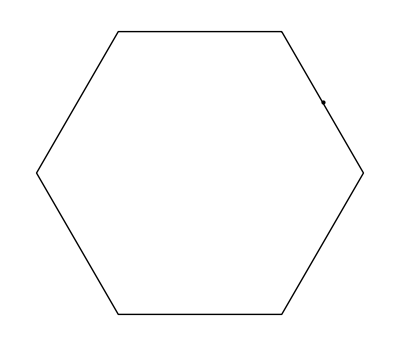

```mathematica
M=MFrac.{b1,b2};
K=KFrac.{b1,b2};
Graphics[{Point[M],Line[Table[RotationMatrix[2Pi/6J].K,{J,0,6}]]}]
```

## 1. S9: Band Dispersions of Untwisted 4QL and 8QL Films

```mathematica
dn=0.01;
Kpath=Join[Table[l K,{l,0.1,0,-0.1/100}],Table[l M,{l,0.1/100,0.1,0.1/100}]];
```

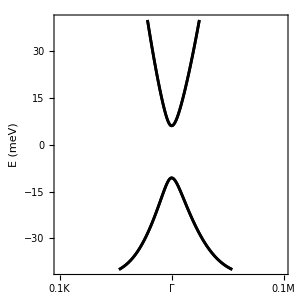

```mathematica
energy=ParallelTable[Sort@Eigenvalues[HSOC4layer[k]],{k,Kpath}];
ListLinePlot[Transpose@energy,{ Frame -> True, FrameLabel -> {"", "E (meV)"}, ImageSize -> 300, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{Automatic,None},{{{1,Style["0.1K",FontSlant->Plain]},{101,Style["Γ",FontSlant->Plain]},{201,Style["0.1M",FontSlant->Plain]},{301,Style["Γ",FontSlant->Plain]}},None}},FrameTicksStyle->Directive[Black,14],FrameStyle->Directive[14,Black],LabelStyle->Directive[14,Black],PlotRange->{-40,40}}]
```

```mathematica
HSOC8layerint=slabHamiltonianlayer[kx,ky,paramsStep2diiExtSOC,8]+KroneckerProduct[IdentityMatrix[8],KroneckerProduct[PauliMatrix[1],IdentityMatrix[2]]]1000000 (kx^2+ky^2)^2;
```

```mathematica
HSOC8layer[{kxx_,kyy_}]:=HSOC8layerint/.{kx->kxx,ky->kyy}
```

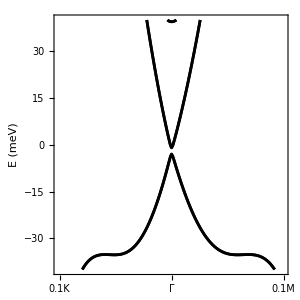

```mathematica
energy=ParallelTable[Sort@Eigenvalues[HSOC8layer[k]],{k,Kpath}];
ListLinePlot[Transpose@energy,{ Frame -> True, FrameLabel -> {"", "E (meV)"}, ImageSize -> 300, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{Automatic,None},{{{1,Style["0.1K",FontSlant->Plain]},{101,Style["Γ",FontSlant->Plain]},{201,Style["0.1M",FontSlant->Plain]},{301,Style["Γ",FontSlant->Plain]}},None}},FrameTicksStyle->Directive[Black,14],FrameStyle->Directive[14,Black],LabelStyle->Directive[14,Black],PlotRange->{-40,40}}]
```

The original energy reference and plot ranges are retained. The original parameters give Gamma-point gaps of approximately 16.67 meV for 4QL and 2.04 meV for 8QL.

## 2. Original Interface-Displacement Data and Fourier Fits

```mathematica
list=Flatten[Table[{m,n},{m,-2,2},{n,-2,2}],1]
```

{{-2,-2},{-2,-1},{-2,0},{-2,1},{-2,2},{-1,-2},{-1,-1},{-1,0},{-1,1},{-1,2},{0,-2},{0,-1},{0,0},{0,1},{0,2},{1,-2},{1,-1},{1,0},{1,1},{1,2},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
Select2[{a_,b_}]:=If[Norm[a b1 + b b2]<=Norm[b1+b2],{a,b},Null]
```

```mathematica
mpairs=DeleteCases[Map[Select2,list],Null]
```

{{-2,1},{-1,-1},{-1,0},{-1,1},{-1,2},{0,-1},{0,0},{0,1},{1,-2},{1,-1},{1,0},{1,1},{2,-1}}

```mathematica
dd0Data31={{0,0,-85.91445520451418},{1/3,2/3,-69.57137634548101},{2/3,1/3,-65.79731552468503},{1/3,1/3,-50.37555797576074}};
dd1Data31={{0,0,2.97},{1/3,2/3,-44.850276555519955},{2/3,1/3,-21.483275602258804},{1/3,1/3,-41.541090407884134}};
dd3Data31={{0,0,-8.373},{1/3,2/3,-9.899117401569661},{2/3,1/3,14.786098376115142},{1/3,1/3,-171.5627652020457}};
dC0t1QLData31={{0,0,0.0},{1/3,2/3,46.01559725746091},{2/3,1/3,70.88603610706494},{1/3,1/3,42.059351906329894}};
dC0t3QLIntData31={{0,0,0.0},{1/3,2/3,17.934538134449966},{2/3,1/3,39.788335829168496},{1/3,1/3,62.76208681292542}};
dataall31={dd0Data31,dd1Data31,dd3Data31,dC0t1QLData31,dC0t3QLIntData31};
```

```mathematica
Clear@f
```

```mathematica
fd[{x_,y_}]:=a+(Rb+I Ib)Total@Table[Exp[(I RotationMatrix[2Pi/3 j]. b1).{x,y}],{j,0,2}]+(Rb-I Ib)Total@Table[Exp[-(I RotationMatrix[2Pi/3 j]. b1).{x,y}],{j,0,2}]+(c)Total@Table[Exp[-(I RotationMatrix[2Pi/6 j]. (b1+b2)).{x,y}],{j,0,5}]//FullSimplify//Chop
```

```mathematica
transferr[{x_,y_}]:=x a1+y a2
```

```mathematica
listd=Map[transferr,dd0Data31 [[;;,{1,2}]]]
```

{{0.,0.},{0.,2.38908},{2.069,1.19454},{0.689667,1.19454}}

```mathematica
Fouriercolist=Table[Solve[Map[fd,listd]-dataall31[[i]] [[;;,3]]==0,{a,Rb,Ib,c}],{i,1,5}];
```

```mathematica
Fouriercolistdicts=Association/@Flatten[Fouriercolist,1]
```

{<|a→-58.1707,Rb→-2.02557,Ib→0.363159,c→-2.59839|>,<|a→-34.7345,Rb→4.0152,Ib→2.24849,c→2.26888|>,<|a→-114.763,Rb→-1.20183,Ib→2.37534,c→18.9334|>,<|a→41.0286,Rb→-6.49454,Ib→2.39316,c→-0.343571|>,<|a→48.255,Rb→-3.20683,Ib→2.10288,c→-4.83568|>}

```mathematica
paramDict=AssociationThread[{"DD0","DD1","DD3","dC0t1QL","dC0t3QL"},Association/@Flatten[Fouriercolistdicts,1]]
```

<|DD0→<|a→-58.1707,Rb→-2.02557,Ib→0.363159,c→-2.59839|>,DD1→<|a→-34.7345,Rb→4.0152,Ib→2.24849,c→2.26888|>,DD3→<|a→-114.763,Rb→-1.20183,Ib→2.37534,c→18.9334|>,dC0t1QL→<|a→41.0286,Rb→-6.49454,Ib→2.39316,c→-0.343571|>,dC0t3QL→<|a→48.255,Rb→-3.20683,Ib→2.10288,c→-4.83568|>|>

```mathematica
couplingmatrixd0=Table[0,{i,1,3*4},{j,1,4}];
couplingmatrixd0[[-2,1]]=couplingmatrixd0[[-1,2]]=1;
couplingmatrixd1=Table[0,{i,1,3*4},{j,1,4}];
Table[couplingmatrixd1[[2*4+i,i]]=1,{i,1,4}];
couplingmatrixd3=Table[0,{i,1,3*4},{j,1,4}];
couplingmatrixd3[[2*4+2,4]]=couplingmatrixd3[[2*4+1,3]]=1;
```

```mathematica
modePairs={{-2,1},{-1,-1},{-1,0},{-1,1},{-1,2},{0,-1},{0,0},{0,1},{1,-2},{1,-1},{1,0},{1,1},{2,-1}};dd0CoeffMN={paramDict["DD0"][c],paramDict["DD0"][c],paramDict["DD0"][Rb]-I paramDict["DD0"][Ib],paramDict["DD0"][Rb]+I paramDict["DD0"][Ib],paramDict["DD0"][c],paramDict["DD0"][Rb]+I paramDict["DD0"][Ib],paramDict["DD0"][a],paramDict["DD0"][Rb]-I paramDict["DD0"][Ib],paramDict["DD0"][c],paramDict["DD0"][Rb]-I paramDict["DD0"][Ib],paramDict["DD0"][Rb]+I paramDict["DD0"][Ib],paramDict["DD0"][c],paramDict["DD0"][c]};dd1CoeffMN={paramDict["DD1"][c],paramDict["DD1"][c],paramDict["DD1"][Rb]-I paramDict["DD1"][Ib],paramDict["DD1"][Rb]+I paramDict["DD1"][Ib],paramDict["DD1"][c],paramDict["DD1"][Rb]+I paramDict["DD1"][Ib],paramDict["DD1"][a],paramDict["DD1"][Rb]-I paramDict["DD1"][Ib],paramDict["DD1"][c],paramDict["DD1"][Rb]-I paramDict["DD1"][Ib],paramDict["DD1"][Rb]+I paramDict["DD1"][Ib],paramDict["DD1"][c],paramDict["DD1"][c]};
dd3CoeffMN={paramDict["DD3"][c],paramDict["DD3"][c],paramDict["DD3"][Rb]-I paramDict["DD3"][Ib],paramDict["DD3"][Rb]+I paramDict["DD3"][Ib],paramDict["DD3"][c],paramDict["DD3"][Rb]+I paramDict["DD3"][Ib],paramDict["DD3"][a],paramDict["DD3"][Rb]-I paramDict["DD3"][Ib],paramDict["DD3"][c],paramDict["DD3"][Rb]-I paramDict["DD3"][Ib],paramDict["DD3"][Rb]+I paramDict["DD3"][Ib],paramDict["DD3"][c],paramDict["DD3"][c]};dC0t1QLCoeffMN={paramDict["dC0t1QL"][c],paramDict["dC0t1QL"][c],paramDict["dC0t1QL"][Rb]-I paramDict["dC0t1QL"][Ib],paramDict["dC0t1QL"][Rb]+I paramDict["dC0t1QL"][Ib],paramDict["dC0t1QL"][c],paramDict["dC0t1QL"][Rb]+I paramDict["dC0t1QL"][Ib],paramDict["dC0t1QL"][a],paramDict["dC0t1QL"][Rb]-I paramDict["dC0t1QL"][Ib],paramDict["dC0t1QL"][c],paramDict["dC0t1QL"][Rb]-I paramDict["dC0t1QL"][Ib],paramDict["dC0t1QL"][Rb]+I paramDict["dC0t1QL"][Ib],paramDict["dC0t1QL"][c],paramDict["dC0t1QL"][c]};
dC0t3QLCoeffMN={paramDict["dC0t3QL"][c],paramDict["dC0t3QL"][c],paramDict["dC0t3QL"][Rb]-I paramDict["dC0t3QL"][Ib],paramDict["dC0t3QL"][Rb]+I paramDict["dC0t3QL"][Ib],paramDict["dC0t3QL"][c],paramDict["dC0t3QL"][Rb]+I paramDict["dC0t3QL"][Ib],paramDict["dC0t3QL"][a],paramDict["dC0t3QL"][Rb]-I paramDict["dC0t3QL"][Ib],paramDict["dC0t3QL"][c],paramDict["dC0t3QL"][Rb]-I paramDict["dC0t3QL"][Ib],paramDict["dC0t3QL"][Rb]+I paramDict["dC0t3QL"][Ib],paramDict["dC0t3QL"][c],paramDict["dC0t3QL"][c]};
```

## 3. Single-Angle 3+1 Moire Hamiltonian: E2 / S10 / S11

```mathematica
HSOC3layerint=HSOC4layer[{kx,ky}][[1;;12,1;;12]];
HSOC3layer[{kxx_,kyy_}]:=HSOC3layerint/.{kx->kxx,ky->kyy};
HSOC1layerint=HSOC4layer[{kx,ky}][[1;;4,1;;4]];
HSOC1layer[{kxx_,kyy_}]:=HSOC1layerint/.{kx->kxx,ky->kyy};HNonSOC1layerint=slabHamiltonianDD0k2[kx,ky,params4QLNoSOCDD0k2][[1;;4,1;;4]]+KroneckerProduct[PauliMatrix[1],IdentityMatrix[2]]1000000 (kx^2+ky^2)^2;HNonSOClayer[{kxx_,kyy_}]:=HNonSOC1layerint/.{kx->kxx,ky->kyy}
```

Note: Parameterize the twist angle and G-shell cutoff; retain the original calculation.

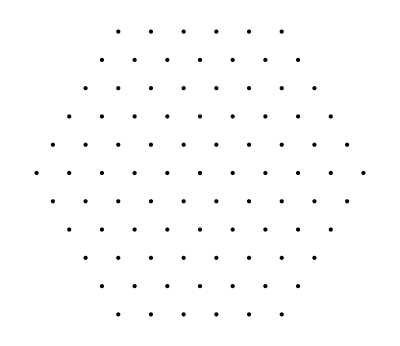

```mathematica
TA=theta31 Degree;bb1=RotationMatrix[2Pi/4].b1*TA;bb2=RotationMatrix[2Pi/4].b2*TA;bb3=RotationMatrix[2Pi/3].bb1;bb4=RotationMatrix[2Pi/3].bb3//Chop;bb5=RotationMatrix[2Pi/3].bb4//Chop;bb6=RotationMatrix[2Pi/3].bb5//Chop;n=moireShell;Glength=Join[Table[i,{i,n+1,2n}],{2n+1},Table[i,{i,2n,n+1,-1}]];Gbegin=Table[Total@Glength[[1;;i]]-Glength[[i]]+1,{i,1,Length[Glength]}];G=Join[ArrayFlatten[Table[(n-i)bb5+j bb4,{i,0,n},{j,-i,n}],1],ArrayFlatten[Table[(-i)bb5+j bb4,{i,1,n},{j,-n,n-i}],1]];Graphics[Point[G]]
```

```mathematica
off=Table[ConstantArray[0,{Total@Glength,Total@Glength}],{i,1,13}];Table[Table[If[Norm[G[[i]]-G[[j]]-mpairs[[k]].{bb1,bb2}]<=Norm[bb1]/100,off[[k]][[i,j]]=1],{i,1,Total@Glength},{j,1,Total@Glength}],{k,1,13}];
```

```mathematica
Hoffmoire=Total@ParallelTable[KroneckerProduct[off[[i]],couplingmatrixd0*dd0CoeffMN[[i]]
+couplingmatrixd1*dd1CoeffMN[[i]]
+couplingmatrixd3*dd3CoeffMN[[i]]],{i,1,13}];
```

```mathematica
H3Int=Normal@BlockDiagonalMatrix@ParallelTable[ HSOC3layer[{kx,ky}+G[[i]]],{i,1,Total@Glength}];H3diag[{kxx_,kyy_}]:=N@Chop@H3Int/.{kx->kxx,ky->kyy};H1Int=Normal@BlockDiagonalMatrix@ParallelTable[ HSOC1layer[{kx,ky}+G[[i]]],{i,1,Total@Glength}];H1diag[{kxx_,kyy_}]:=N@Chop@H1Int/.{kx->kxx,ky->kyy};
H1nsocInt=Normal@BlockDiagonalMatrix@ParallelTable[ HNonSOClayer[{kx,ky}+G[[i]]],{i,1,Total@Glength}];
H1nsocdiag[{kxx_,kyy_}]:=N@Chop@H1nsocInt/.{kx->kxx,ky->kyy};
```

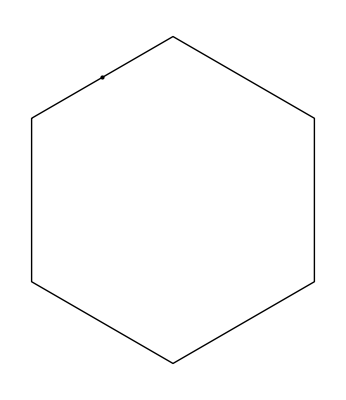

```mathematica
mM=MFrac.{bb1,bb2};
mK=KFrac.{bb1,bb2};
Graphics[{Point[mM],Line[Table[RotationMatrix[2Pi/6J].mK,{J,0,6}]]}]
```

```mathematica
couplingVterm1={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
couplingVterm3=Join[Table[0,{i,1,8}],Table[1,{i,1,4}]]//DiagonalMatrix;
```

```mathematica
HoffmoireC3=Total@ParallelTable[KroneckerProduct[off[[i]],couplingVterm3*dC0t3QLCoeffMN[[i]]],{i,1,13}];HoffmoireC1=Total@ParallelTable[KroneckerProduct[off[[i]],couplingVterm1*dC0t1QLCoeffMN[[i]]],{i,1,13}];
```

```mathematica
D1=(H3diag[{kx,ky}]//Dimensions)[[1]];D2=D1/3;
cp=DiagonalMatrix@Join[ Table[0,{i,1,D1}],Table[1,{i,1,D2}]];
```

```mathematica
Hallint=ArrayFlatten[{{H3diag[{kx,ky}]+lm HoffmoireC3,lm Hoffmoire},{lm Conjugate@Transpose@Hoffmoire,H1diag[{kx,ky}]+lm HoffmoireC1}}];Hall[{kxx_,kyy_},lmm_,mu_]:=(N@Chop@Hallint/.{kx->kxx,ky->kyy,lm->lmm})+mu cp
```

```mathematica
dn=0.01;
mKpath=Join[Table[l mK,{l,-1,0,dn}],Table[l mM,{l,dn,1,dn}]];
```

```mathematica
Plotstyle={ Frame -> True, ImageSize -> Large, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{Automatic,None},{{{1,"K"},{101,"Γ"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,24],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[20,Black]};
```

```mathematica
DimH3=Dimensions[Hall[{0,0},1,0]][[1]]/4*3
```

1092

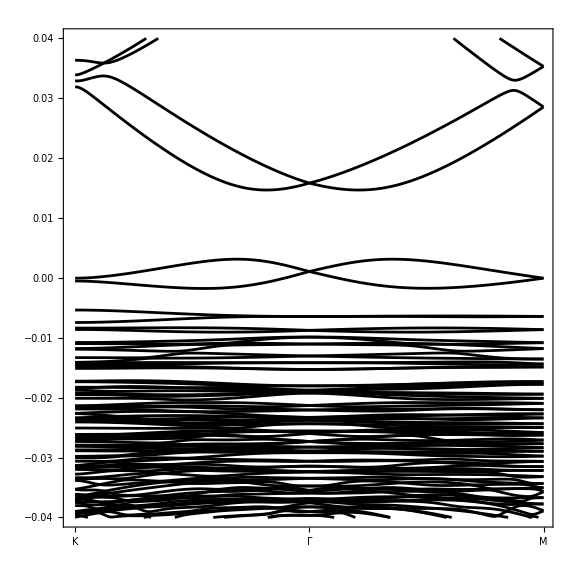

```mathematica
energy=ParallelTable[Sort@Eigenvalues[Hall[k,1,0]],{k,mKpath}];
P2=ListLinePlot[Transpose@energy/1000,PlotRange->{-0.04,0.04},Plotstyle]
```

The band plot above retains the original division by 1000, so its energy values are in eV. The unfolded spectra below use meV, as in the original code.

## 4. Original Unfolding Functions and Single-Angle 3+1 Spectra

The complete original code_yunzhe_newP4_unfolding.wl is embedded below. The unfolding weights and spectral-function formulas are retained.

```mathematica
ClearAll[sortEigensystemByEnergy,lorentzianKernel,kLorentzianKernel,kDiskSamples,gSectorIndices,unfoldedWeight,externalKPathIndex,foldExternalK,foldExternalKPath,eigensystemAtFoldedK,unfoldedSpectrumAtAlignedK,unfoldedSpectralDataAligned,unfoldedSpectralDensityPlotAligned,unfoldedSpectrumAtKWithKBroadening,unfoldedSpectralDataKBroadening,unfoldedSpectralDensityPlotKBroadening,shiftEigenvaluesByHalfFilling];sortEigensystemByEnergy[{vals_,vecs_}]:=Transpose[SortBy[Transpose[{vals,vecs}],First]];lorentzianKernel[e_,e0_,eta_]:=eta/(π ((e-e0)^2+eta^2));kLorentzianKernel[dk_,etaK_]:=etaK/(π (dk^2+etaK^2));kDiskSamples[k0_,kr_,kdens_]:=If[TrueQ[kr==0],{k0},Select[Flatten[Table[k0+{dx,dy},{dx,-kr,kr,kr/kdens},{dy,-kr,kr,kr/kdens}],1],Norm[#1-k0]≤kr&]];externalKPathIndex[kPath_]:=Prepend[Accumulate[Norm/@Differences[kPath]],0];foldExternalK[kExt_,gList_:G]:=Module[{best},best=First[MinimalBy[MapIndexed[{Norm[kExt-#1],#2⟦1⟧,#1}&,gList],First]];Association["KFold"->kExt-best⟦3⟧,"GIndex"->best⟦2⟧,"G"->best⟦3⟧,"Distance"->best⟦1⟧]];foldExternalKPath[kExtPath_,gList_:G]:=Module[{fold=(foldExternalK[#1,gList]&)/@kExtPath},Association["KFoldPath"->(#1["KFold"]&)/@fold,"GIndexPath"->(#1["GIndex"]&)/@fold,"GPath"->(#1["G"]&)/@fold,"FoldInfo"->fold]];gSectorIndices[gIndex_,blockSpec_List]:=Flatten[blockSpec/.{offset_,blockDim_,subinds_}:>offset+(gIndex-1) blockDim+subinds];unfoldedWeight[vec_,gIndex_,blockSpec_]:=Module[{inds,v,validInds,mask},inds=gSectorIndices[gIndex,blockSpec];v=If[Head[vec]===SparseArray,Normal[vec],vec];validInds=Select[inds,IntegerQ[#1]&&1≤#1≤Length[v]&];If[Length[validInds]==0,0.,mask=Normal[SparseArray[Thread[validInds->1.],Length[v]]];Total[Abs[v]^2 mask]]];eigensystemAtFoldedK[hFun_,kFold_,nEig_:All]:=sortEigensystemByEnergy[If[nEig===All,Eigensystem[hFun[kFold]],Eigensystem[hFun[kFold],nEig]]];shiftEigenvaluesByHalfFilling[vals_,shift_:False]:=Module[{nOcc},Which[TrueQ[shift],nOcc=Floor[Length[vals]/2];vals-vals⟦nOcc⟧,NumericQ[shift],vals-shift,True,vals]];unfoldedSpectrumAtAlignedK[vals_,vecs_,gIndex_,eGrid_,eta_,blockSpec_List]:=Module[{weights},weights=(unfoldedWeight[#1,gIndex,blockSpec]&)/@vecs;Table[Total[weights (lorentzianKernel[e,#1,eta]&)/@vals],{e,eGrid}]];unfoldedSpectralDataAligned[kExtPath_,evalsByK_,evecsByK_,gIndexPath_,eGrid_,eta_,blockSpec_List]:=Module[{x=externalKPathIndex[kExtPath],spectra},spectra=Table[unfoldedSpectrumAtAlignedK[evalsByK⟦ik⟧,evecsByK⟦ik⟧,gIndexPath⟦ik⟧,eGrid,eta,blockSpec],{ik,Length[kExtPath]}];Flatten[Table[{x⟦ik⟧,eGrid⟦ie⟧,spectra⟦ik,ie⟧},{ik,Length[x]},{ie,Length[eGrid]}],1]];unfoldedSpectralDensityPlotAligned[kExtPath_,evalsByK_,evecsByK_,gIndexPath_,eGrid_,eta_,blockSpec_List,opts:OptionsPattern[ListDensityPlot]]:=ListDensityPlot[unfoldedSpectralDataAligned[kExtPath,evalsByK,evecsByK,gIndexPath,eGrid,eta,blockSpec],InterpolationOrder->1,Frame->True,FrameLabel->{"external k path","E","A(k,E)"},PlotLegends->Automatic,opts];unfoldedSpectrumAtKWithKBroadening[kExt_,hFun_,eGrid_,etaE_,etaK_,kr_,kdens_,blockSpec_List,gList_:G,nEig_:All,energyShift_:False]:=Module[{ksamples,normaliz,spectrum,fold,eig,vals,vecs,weights,weightK},ksamples=kDiskSamples[kExt,kr,kdens];normaliz=0.;spectrum=ConstantArray[0.,Length[eGrid]];Do[fold=foldExternalK[ksamp,gList];weightK=kLorentzianKernel[Norm[ksamp-kExt],etaK];normaliz+=weightK;eig=eigensystemAtFoldedK[hFun,fold["KFold"],nEig];vals=shiftEigenvaluesByHalfFilling[eig⟦1⟧,energyShift];vecs=eig⟦2⟧;weights=(unfoldedWeight[#1,fold["GIndex"],blockSpec]&)/@vecs;spectrum+=weightK Table[Total[weights (lorentzianKernel[e,#1,etaE]&)/@vals],{e,eGrid}],{ksamp,ksamples}];spectrum/normaliz];unfoldedSpectralDataKBroadening[kExtPath_,hFun_,eGrid_,etaE_,etaK_,kr_,kdens_,blockSpec_List,gList_:G,nEig_:All,energyShift_:False]:=Module[{x=externalKPathIndex[kExtPath],spectra},spectra=ParallelTable[unfoldedSpectrumAtKWithKBroadening[kExtPath⟦ik⟧,hFun,eGrid,etaE,etaK,kr,kdens,blockSpec,gList,nEig,energyShift],{ik,Length[kExtPath]}];Flatten[Table[{x⟦ik⟧,eGrid⟦ie⟧,spectra⟦ik,ie⟧},{ik,Length[x]},{ie,Length[eGrid]}],1]];unfoldedSpectralDensityPlotKBroadening[kExtPath_,hFun_,eGrid_,etaE_,etaK_,kr_,kdens_,blockSpec_List,gList_:G,nEig_:All,energyShift_:False,opts:OptionsPattern[ListDensityPlot]]:=ListDensityPlot[unfoldedSpectralDataKBroadening[kExtPath,hFun,eGrid,etaE,etaK,kr,kdens,blockSpec,gList,nEig,energyShift],InterpolationOrder->1,Frame->True,FrameLabel->{"external k path","E","A(k,E)"},PlotLegends->Automatic,opts];
```

```mathematica
blockSpec31All={{0,12,Range[12]},{DimH3,4,Range[4]}};
```

```mathematica
kExtPath31Four = Join[
  Table[l  0.1K, {l, 1, 0, -0.01}],
  Table[l  0.1M, {l, 0.01, 1, 0.01}]
];fold31Four = foldExternalKPath[kExtPath31Four, G];
kFoldPath31Four = fold31Four["KFoldPath"];
gIndexPath31Four = fold31Four["GIndexPath"];
```

```mathematica
Clear@eigsys31Four
```

```mathematica
If[! ValueQ[eigsys31Four],
  eigsys31Four =
    sortEigensystemByEnergy /@
      ParallelTable[
        Eigensystem[Hall[k, 1, 0], -100],
        {k, kFoldPath31Four}
      ];
];
evals31Four = eigsys31Four[[All, 1]];
evecs31Four = eigsys31Four[[All, 2]];

eGrid31Four = Range[-40, 40, 0.5];
eta31Four = 1.0;
```

```mathematica
FourAll =unfoldedSpectralDataAligned[
    kExtPath31Four, evals31Four, evecs31Four, gIndexPath31Four, eGrid31Four, eta31Four, blockSpec31All
  ];
```

```mathematica
ListDensityPlot[FourAll,
  InterpolationOrder -> 1,
  Frame -> True,
  FrameLabel -> {"", "E", "A(k,E)"},
  PlotLegends -> Automatic,ColorFunction -> "AvocadoColors",PlotRange -> All,FrameTicks->{{Automatic,Automatic},{{{0,"0.1K"},{0.1K//Norm,"Γ"},{FourAll[[;;,1]]//Max,"0.1M"},{3,"Γ"}},Automatic}}
]
```

-Graphics-

## 5. E3: Interface Onsite Potential and Band Inversion at 1 Degree

Rebuild the original 3+1 model at 1 degree so that the choice of theta31 does not affect E3. The calculation uses Hallcp[k,1,mu,mu].

Note: Parameterize the twist angle and G-shell cutoff; retain the original calculation.

```mathematica
TA=1 Degree;bb1=RotationMatrix[2Pi/4].b1*TA;bb2=RotationMatrix[2Pi/4].b2*TA;bb3=RotationMatrix[2Pi/3].bb1;bb4=RotationMatrix[2Pi/3].bb3//Chop;bb5=RotationMatrix[2Pi/3].bb4//Chop;bb6=RotationMatrix[2Pi/3].bb5//Chop;n=moireShell;Glength=Join[Table[i,{i,n+1,2n}],{2n+1},Table[i,{i,2n,n+1,-1}]];Gbegin=Table[Total@Glength[[1;;i]]-Glength[[i]]+1,{i,1,Length[Glength]}];G=Join[ArrayFlatten[Table[(n-i)bb5+j bb4,{i,0,n},{j,-i,n}],1],ArrayFlatten[Table[(-i)bb5+j bb4,{i,1,n},{j,-n,n-i}],1]];Graphics[Point[G]]
```

-Graphics-

```mathematica
off=Table[ConstantArray[0,{Total@Glength,Total@Glength}],{i,1,13}];Table[Table[If[Norm[G[[i]]-G[[j]]-mpairs[[k]].{bb1,bb2}]<=Norm[bb1]/100,off[[k]][[i,j]]=1],{i,1,Total@Glength},{j,1,Total@Glength}],{k,1,13}];
```

```mathematica
Hoffmoire=Total@ParallelTable[KroneckerProduct[off[[i]],couplingmatrixd0*dd0CoeffMN[[i]]
+couplingmatrixd1*dd1CoeffMN[[i]]
+couplingmatrixd3*dd3CoeffMN[[i]]],{i,1,13}];
```

```mathematica
H3Int=Normal@BlockDiagonalMatrix@ParallelTable[ HSOC3layer[{kx,ky}+G[[i]]],{i,1,Total@Glength}];H3diag[{kxx_,kyy_}]:=N@Chop@H3Int/.{kx->kxx,ky->kyy};H1Int=Normal@BlockDiagonalMatrix@ParallelTable[ HSOC1layer[{kx,ky}+G[[i]]],{i,1,Total@Glength}];H1diag[{kxx_,kyy_}]:=N@Chop@H1Int/.{kx->kxx,ky->kyy};
H1nsocInt=Normal@BlockDiagonalMatrix@ParallelTable[ HNonSOClayer[{kx,ky}+G[[i]]],{i,1,Total@Glength}];
H1nsocdiag[{kxx_,kyy_}]:=N@Chop@H1nsocInt/.{kx->kxx,ky->kyy};
```

```mathematica
mM=MFrac.{bb1,bb2};
mK=KFrac.{bb1,bb2};
Graphics[{Point[mM],Line[Table[RotationMatrix[2Pi/6J].mK,{J,0,6}]]}]
```

-Graphics-

```mathematica
couplingVterm1={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
couplingVterm3=Join[Table[0,{i,1,8}],Table[1,{i,1,4}]]//DiagonalMatrix;
```

```mathematica
HoffmoireC3=Total@ParallelTable[KroneckerProduct[off[[i]],couplingVterm3*dC0t3QLCoeffMN[[i]]],{i,1,13}];HoffmoireC1=Total@ParallelTable[KroneckerProduct[off[[i]],couplingVterm1*dC0t1QLCoeffMN[[i]]],{i,1,13}];
```

```mathematica
D1=(H3diag[{kx,ky}]//Dimensions)[[1]];D2=D1/3;
cp=DiagonalMatrix@Join[ Table[0,{i,1,D1}],Table[1,{i,1,D2}]];
```

```mathematica
Hallint=ArrayFlatten[{{H3diag[{kx,ky}]+lm HoffmoireC3,lm Hoffmoire},{lm Conjugate@Transpose@Hoffmoire,H1diag[{kx,ky}]+lm HoffmoireC1}}];Hall[{kxx_,kyy_},lmm_,mu_]:=(N@Chop@Hallint/.{kx->kxx,ky->kyy,lm->lmm})+mu cp
```

```mathematica
dn=0.01;
mKpath=Join[Table[l mK,{l,-1,0,dn}],Table[l mM,{l,dn,1,dn}]];
```

```mathematica
Plotstyle={ Frame -> True, ImageSize -> Large, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{Automatic,None},{{{1,"K"},{101,"Γ"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,24],FrameLabel->{"",""},FrameStyle->Directive[20,Black],LabelStyle->Directive[20,Black]};
```

```mathematica
DimH3=Dimensions[Hall[{0,0},1,0]][[1]]/4*3
```

1092

```mathematica
c3layer=N@Join[Table[0,{i,1,8}],Table[1,{j,1,4}]]//DiagonalMatrix;
```

```mathematica
c1layer=N@Table[1,{j,1,4}]//DiagonalMatrix;
```

```mathematica
H3Intcp=Normal@BlockDiagonalMatrix@ParallelTable[ HSOC3layer[{kx,ky}+G[[i]]]+C3 c3layer,{i,1,Total@Glength}];H3diagcp[{kxx_,kyy_},CC3_]:=N@Chop@H3Intcp/.{kx->kxx,ky->kyy,C3->CC3};H1Intcp=Normal@BlockDiagonalMatrix@ParallelTable[ HSOC1layer[{kx,ky}+G[[i]]]+C1 c1layer,{i,1,Total@Glength}];H1diagcp[{kxx_,kyy_},CC1_]:=N@Chop@H1Intcp/.{kx->kxx,ky->kyy,C1->CC1};
```

```mathematica
Hallintcp=ArrayFlatten[{{H3diagcp[{kx,ky},C3]+lm HoffmoireC3,lm Hoffmoire},{lm Conjugate@Transpose@Hoffmoire,H1diagcp[{kx,ky},C1]+lm HoffmoireC1}}];Hallcp[{kxx_,kyy_},lmm_,CC1_,CC3_]:=(N@Chop@Hallintcp/.{kx->kxx,ky->kyy,lm->lmm,C3->CC3,C1->CC1})
```

Determine the Hamiltonian dimension before calculating gaps or Wilson loops.

```mathematica
DimH=Dimensions[Hallcp[{0,0},1,0,0]]⟦1⟧;
```

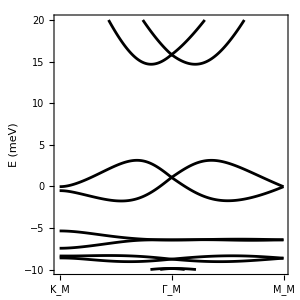

```mathematica
mu=0;energy=ParallelTable[Sort@Eigenvalues[Hallcp[k,1,mu,mu]],{k,mKpath}];P2=ListLinePlot[Transpose@energy,{ Frame -> True, FrameLabel -> {"", "E (meV)"}, ImageSize -> 300, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{Automatic,None},{{{1,Style[Subscript["K","M"],FontSlant->Plain]},{101,Style[Subscript["Γ","M"],FontSlant->Plain]},{201,Style[Subscript["M","M"],FontSlant->Plain]},{301,Style["Γ",FontSlant->Plain]}},None}},FrameTicksStyle->Directive[Black,14],FrameStyle->Directive[14,Black],LabelStyle->Directive[14,Black],PlotRange->{10-20,40-20}}]
```

```mathematica
mu=25.164
```

25.164

```mathematica
energy=ParallelTable[Sort@Eigenvalues[Hallcp[k,1,mu,mu]],{k,mKpath}];
```

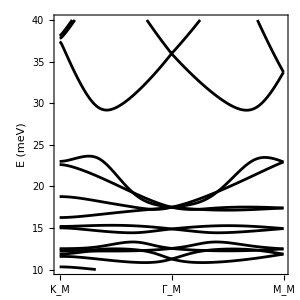

```mathematica
P2=ListLinePlot[Transpose@energy,{ Frame -> True, FrameLabel -> {"", "E (meV)"}, ImageSize -> 300, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{Automatic,None},{{{1,Style[Subscript["K","M"],FontSlant->Plain]},{101,Style[Subscript["Γ","M"],FontSlant->Plain]},{201,Style[Subscript["M","M"],FontSlant->Plain]},{301,Style["Γ",FontSlant->Plain]}},None}},FrameTicksStyle->Directive[Black,14],FrameStyle->Directive[14,Black],LabelStyle->Directive[14,Black],PlotRange->{10,40}}]
```

```mathematica
mu=30
```

30

```mathematica
energy=ParallelTable[Sort@Eigenvalues[Hallcp[k,1,mu,mu]],{k,mKpath}];
```

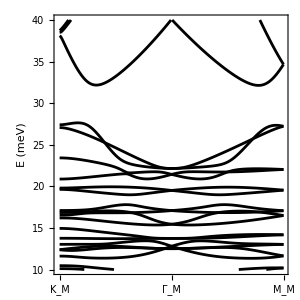

```mathematica
P2=ListLinePlot[Transpose@energy,{ Frame -> True, FrameLabel -> {"", "E (meV)"}, ImageSize -> 300, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{Automatic,None},{{{1,Style[Subscript["K","M"],FontSlant->Plain]},{101,Style[Subscript["Γ","M"],FontSlant->Plain]},{201,Style[Subscript["M","M"],FontSlant->Plain]},{301,Style["Γ",FontSlant->Plain]}},None}},FrameTicksStyle->Directive[Black,14],FrameStyle->Directive[14,Black],LabelStyle->Directive[14,Black],PlotRange->{10,40}}]
```

```mathematica
Gap[mu_]:=Apply[Subtract,Eigenvalues[Hallcp[{0,0},1,mu,mu]+1000 IdentityMatrix[DimH],{DimH/2+2,DimH/2+3}]-1000]
```

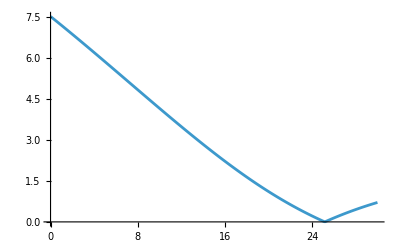

```mathematica
GAP=ParallelTable[{mu,Gap[mu]},{mu,0,30,0.1}];ListLinePlot[GAP]
```

Retain the eigenvalue indices from the original Gap2 cell. Replace the trial linear-layer-potential model Hallcpg with Hallcp[k,1,mu,mu] so that both gap curves use the same interface potential.

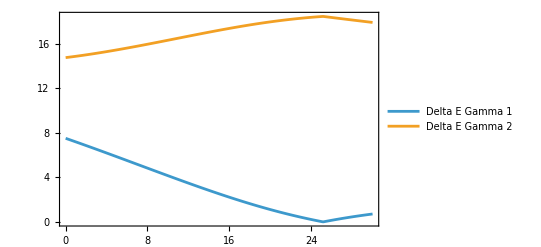

```mathematica
Gap2[mu_]:=Subtract@@(Eigenvalues[Hallcp[{0,0},1,mu,mu]+1000 IdentityMatrix[DimH],{DimH/2,DimH/2+1}]-1000);GAP2=ParallelTable[{mu,Gap2[mu]},{mu,0,30,0.1}];ListLinePlot[{GAP,GAP2},Frame->True,PlotRange->All,PlotLegends->{"Delta E Gamma 1","Delta E Gamma 2"}]
```

## 6. E3: Original Wilson Loop and Wannier-Center Flow

The original INTDOT, Tran2, and WTPBUT calculations are retained, without SVD unitarization. The original grid uses num=100 and num2=200 and can take substantial time.

```mathematica
one12=IdentityMatrix[12];zero12=IdentityMatrix[12]0;
```

```mathematica
one4=IdentityMatrix[4];zero4=IdentityMatrix[4]0;
```

```mathematica
num=100;
B1=bb1;
B2=bb2;
```

```mathematica
Clear@translation22
```

```mathematica
translation22[i_,j_]:=If[G[[i]]==-bb2+G[[j]],one4,zero4];
Tran22=N@ArrayFlatten@Table[translation22[i,k],{i,1,Total@Glength},{k,1,Total@Glength}];
```

```mathematica
translation21[i_,j_]:=If[G[[i]]==-bb2+G[[j]],one12,zero12];
Tran21=N@ArrayFlatten@Table[translation21[i,k],{i,1,Total@Glength},{k,1,Total@Glength}];
```

```mathematica
Tran2=BlockDiagonalMatrix[{Tran21,Tran22}];
```

```mathematica
mu=30
```

```mathematica
DimH=Dimensions[Hallcp[{0,0},1,mu,mu]][[1]]
```

```mathematica
num2=200;INTDOT[k_List]:=Im[Chop@Log[Chop@Eigenvalues[Apply[Dot,Table[Conjugate[k[[i]]].Transpose[k[[i+1]]],{i,1,num2}]]]]]/(2Pi);Irange=Flatten@Append[Table[i,{i,0,num2-1}],0];WTPBUT[a_]:=With[{t=ParallelTable[EigPB[ a/num B1+i/num2 B2],{i,0,num2-1}]},
INTDOT[Append[t,Transpose[Tran2.Transpose[t[[1]]]]]]];
```

```mathematica
EigPB[k_List]:=Eigenvectors[Hallcp[k,1,mu,mu]+1000 IdentityMatrix[DimH],{DimH/2+1,DimH/2+2}]
```

```mathematica
wloopPBUT=Table[WTPBUT[n ],{n,0,num}];
```

```mathematica
ListPlot[Transpose@wloopPBUT,PlotStyle->{{PointSize[0.012],Black}},Frame->True,PlotRange->{-0.5,0.5},FrameTicks->{{{-0.5,0.5},None},{{{1,"Γ"},{1+num/2,"M"},{1+num,"Γ"},{14,""}},None}},FrameTicksStyle->Directive[Black,20],AspectRatio->1]
```

```mathematica
EigPB[k_List]:=Eigenvectors[Hallcp[k,1,0,0]+1000 IdentityMatrix[DimH],{DimH/2+1,DimH/2+2}]
```

```mathematica
wloopPBUT=Table[WTPBUT[n ],{n,0,num}];
```

```mathematica
ListPlot[Transpose@wloopPBUT,PlotStyle->{{PointSize[0.012],Black}},Frame->True,PlotRange->{-0.5,0.5},FrameTicks->{{{-0.5,0.5},None},{{{1,"Γ"},{1+num/2,"M"},{1+num,"Γ"},{14,""}},None}},FrameTicksStyle->Directive[Black,20],AspectRatio->1]
```

## 7. S13: The 3+5 Model at 1 Degree and Three Layer Projections

```mathematica
HSOC5layerint=slabHamiltonianlayer[kx,ky,paramsStep2diiExtSOC,5]+KroneckerProduct[IdentityMatrix[5],KroneckerProduct[PauliMatrix[1],IdentityMatrix[2]]]1000000 (kx^2+ky^2)^2;
```

```mathematica
HSOC5layer[{kxx_,kyy_}]:=HSOC5layerint/.{kx->kxx,ky->kyy}
```

```mathematica
zero1216=Table[0,{i,1,12},{j,1,16}];
```

```mathematica
HNSOC5layerint=ArrayFlatten[{{HNonSOClayer[{kx,ky}],HSOC5layer[{kx,ky}][[1;;4,5;;20]]},{HSOC5layer[{kx,ky}][[5;;20,1;;4]],HSOC5layer[{kx,ky}][[5;;20,5;;20]]}}];
```

```mathematica
HNSOC5layer[{kxx_,kyy_}]:=HNSOC5layerint/.{kx->kxx,ky->kyy}
```

Note: Fix the twist angle at 1 degree and replace n=5 with moireShell.

```mathematica
TA=1 Degree;bb1=RotationMatrix[2Pi/4].b1*TA;bb2=RotationMatrix[2Pi/4].b2*TA;bb3=RotationMatrix[2Pi/3].bb1;bb4=RotationMatrix[2Pi/3].bb3//Chop;bb5=RotationMatrix[2Pi/3].bb4//Chop;bb6=RotationMatrix[2Pi/3].bb5//Chop;n=moireShell;Glength=Join[Table[i,{i,n+1,2n}],{2n+1},Table[i,{i,2n,n+1,-1}]];Gbegin=Table[Total@Glength[[1;;i]]-Glength[[i]]+1,{i,1,Length[Glength]}];G=Join[ArrayFlatten[Table[(n-i)bb5+j bb4,{i,0,n},{j,-i,n}],1],ArrayFlatten[Table[(-i)bb5+j bb4,{i,1,n},{j,-n,n-i}],1]];Graphics[Point[G]]
```

-Graphics-

```mathematica
off=Table[ConstantArray[0,{Total@Glength,Total@Glength}],{i,1,13}];Table[Table[If[Norm[G[[i]]-G[[j]]-mpairs[[k]].{bb1,bb2}]<=Norm[bb1]/100,off[[k]][[i,j]]=1],{i,1,Total@Glength},{j,1,Total@Glength}],{k,1,13}];
```

```mathematica
mM=MFrac.{bb1,bb2};
mK=KFrac.{bb1,bb2};
dn=0.01;
mKpath=Join[Table[l mK,{l,-1,0,dn}],Table[l mM,{l,dn,1,dn}]];
Graphics[{Point[mM],Line[Table[RotationMatrix[2Pi/6J].mK,{J,0,6}]]}]
```

-Graphics-

```mathematica
couplingmatrixd0=Table[0,{i,1,3*4},{j,1,4}];
couplingmatrixd0[[-2,1]]=couplingmatrixd0[[-1,2]]=1;
couplingmatrixd1=Table[0,{i,1,3*4},{j,1,4}];
Table[couplingmatrixd1[[2*4+i,i]]=1,{i,1,4}];
couplingmatrixd3=Table[0,{i,1,3*4},{j,1,4}];
couplingmatrixd3[[2*4+2,4]]=couplingmatrixd3[[2*4+1,3]]=1;
```

```mathematica
couplingmatrixd053=ArrayFlatten[{{couplingmatrixd0,zero1216}}];
couplingmatrixd153=ArrayFlatten[{{couplingmatrixd1,zero1216}}];couplingmatrixd353=ArrayFlatten[{{couplingmatrixd3,zero1216}}];
```

```mathematica
couplingVterm3=Join[Table[0,{i,1,8}],Table[1,{i,1,4}]]//DiagonalMatrix;couplingVterm5=Join[Table[1,{i,1,4}],Table[0,{i,1,16}]]//DiagonalMatrix;
```

```mathematica
H3Int=Normal@BlockDiagonalMatrix@ParallelTable[ HSOC3layer[{kx,ky}+G[[i]]],{i,1,Total@Glength}];H3diag[{kxx_,kyy_}]:=N@Chop@H3Int/.{kx->kxx,ky->kyy};H5Int=Normal@BlockDiagonalMatrix@ParallelTable[ HSOC5layer[{kx,ky}+G[[i]]],{i,1,Total@Glength}];H5diag[{kxx_,kyy_}]:=N@Chop@H5Int/.{kx->kxx,ky->kyy};
H5NInt=Normal@BlockDiagonalMatrix@ParallelTable[ HNSOC5layer[{kx,ky}+G[[i]]],{i,1,Total@Glength}];H5Ndiag[{kxx_,kyy_}]:=N@Chop@H5NInt/.{kx->kxx,ky->kyy};
```

```mathematica
HoffmoireC3=Total@ParallelTable[KroneckerProduct[off[[i]],couplingVterm3*dC0t3QLCoeffMN[[i]]],{i,1,13}];HoffmoireC5=Total@ParallelTable[KroneckerProduct[off[[i]],couplingVterm5*dC0t1QLCoeffMN[[i]]],{i,1,13}];;
```

```mathematica
Hoffmoire53=Total@ParallelTable[KroneckerProduct[off[[i]],couplingmatrixd053*dd0CoeffMN[[i]]
+couplingmatrixd153*dd1CoeffMN[[i]]
+couplingmatrixd353*dd3CoeffMN[[i]]],{i,1,13}];
```

```mathematica
D1=(H3diag[{kx,ky}]//Dimensions)[[1]];D5=D1/3*5;
cp53=DiagonalMatrix@Join[ Table[0,{i,1,D1}],Table[1,{i,1,D5}]];
```

```mathematica
Hallint53=ArrayFlatten[{{H3diag[{kx,ky}]+lm HoffmoireC3,lm Hoffmoire53},{lm Conjugate@Transpose@Hoffmoire53,H5diag[{kx,ky}]+lm HoffmoireC5}}];Hall53[{kxx_,kyy_},lmm_,mu_]:=(N@Chop@Hallint53/.{kx->kxx,ky->kyy,lm->lmm})+mu cp53
```

```mathematica
energy=ParallelTable[Sort@Eigenvalues[Hall53[k,1,0]],{k,mKpath}];
```

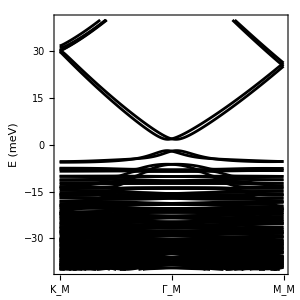

```mathematica
P2=ListLinePlot[Transpose@energy,{ Frame -> True, FrameLabel -> {"", "E (meV)"}, ImageSize -> 300, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{Automatic,None},{{{1,Style[Subscript["K","M"],FontSlant->Plain]},{101,Style[Subscript["Γ","M"],FontSlant->Plain]},{201,Style[Subscript["M","M"],FontSlant->Plain]},{301,Style["Γ",FontSlant->Plain]}},None}},FrameTicksStyle->Directive[Black,14],FrameStyle->Directive[14,Black],LabelStyle->Directive[14,Black],PlotRange->{-40,40}}]
```

```mathematica
blockSpec53top={{0,12,Range[12]}};
```

```mathematica
kExtPath53=Join[Table[l 0.1K,{l,1,0,-dn}],Table[l 0.1M,{l,dn,1,dn}]];
fold53=foldExternalKPath[kExtPath53,G];
kFoldPath53=fold53["KFoldPath"];
gIndexPath53=fold53["GIndexPath"];
```

```mathematica
eigsys53=sortEigensystemByEnergy/@ParallelTable[Eigensystem[Hall53[k,1,0],-500],{k,kFoldPath53}];evals53=eigsys53[[All,1]];
evecs53=eigsys53[[All,2]];
```

```mathematica
eGrid53=Range[-40,40,0.5];
eta53=1.0;
```

```mathematica
totalG53=Total@Glength;
dimTop53=12 totalG53;

blockSpec53All={{0,12,Range[12]},{dimTop53,20,Range[20]}};
```

```mathematica
blockSpec53toptop={{0,12,{1,2,3,4}}}
```

{{0,12,{1,2,3,4}}}

```mathematica
A53All =unfoldedSpectralDataAligned[
    kExtPath53, evals53, evecs53, gIndexPath53, eGrid53, eta53, blockSpec53All
  ];
```

```mathematica
A53Top =unfoldedSpectralDataAligned[
    kExtPath53, evals53, evecs53, gIndexPath53, eGrid53, eta53, blockSpec53top
  ];
```

```mathematica
A53TopTop=unfoldedSpectralDataAligned[
    kExtPath53, evals53, evecs53, gIndexPath53, eGrid53, eta53, blockSpec53toptop
  ];
```

Note: Use A53All for this plot's horizontal range, removing its dependence on another plot's data.

```mathematica
ListDensityPlot[A53All,
  Frame -> True,
FrameLabel->{Style["",FontSize->18],Style["E (meV)",FontSize->18],Style["A(k,E)",FontSize->18]},
  PlotLegends -> Automatic,ColorFunction -> "AvocadoColors",PlotRange -> All,FrameTicks->{{Automatic,Automatic},{{{0,"0.1K"},{0.1K//Norm,"Γ"},{A53All[[;;,1]]//Max,"0.1M"},{3,"Γ"}},Automatic}}
,ImageSize->300,FrameTicksStyle->Directive[Black,14],
LabelStyle->Directive[Black,14]]
```

-Graphics-

Note: Use this plot's own data for its horizontal range.

```mathematica
ListDensityPlot[A53Top,
  Frame -> True,
FrameLabel->{Style["",FontSize->18],Style["E (meV)",FontSize->18],Style["A(k,E)",FontSize->18]},
  PlotLegends -> Automatic,ColorFunction -> "AvocadoColors",PlotRange -> All,FrameTicks->{{Automatic,Automatic},{{{0,"0.1K"},{0.1K//Norm,"Γ"},{A53Top[[;;,1]]//Max,"0.1M"},{3,"Γ"}},Automatic}}
,ImageSize->200,FrameTicksStyle->Directive[Black,14],
LabelStyle->Directive[Black,14]]
```

-Graphics-

Note: Use this plot's own data for its horizontal range.

```mathematica
ListDensityPlot[A53TopTop,
  Frame -> True,
FrameLabel->{Style["",FontSize->18],Style["E (meV)",FontSize->18],Style["A(k,E)",FontSize->18]},
  PlotLegends -> Automatic,ColorFunction -> "AvocadoColors",PlotRange -> All,FrameTicks->{{Automatic,Automatic},{{{0,"0.1K"},{0.1K//Norm,"Γ"},{A53Top[[;;,1]]//Max,"0.1M"},{3,"Γ"}},Automatic}}
,ImageSize->200,FrameTicksStyle->Directive[Black,14],
LabelStyle->Directive[Black,14]]
```

-Graphics-

## 8. S12: Original Weighted Averaging of Existing Angle-Resolved Spectra

This section reads existing spectra without calculating additional angles. It retains the original Transform1, Interpolation, p, and weighted sum. The Export cell that would overwrite average angle.csv is omitted.

```mathematica
Transform1[{a_,b_}]:={(a-80)/10,b};data=Import[FileNameJoin[{NotebookDirectory[],"peakfit - Sheet1.csv"}]];bcClean=Map[Transform1,Select[data[[2;;,{2,3}]],VectorQ[#,NumericQ]&]];
```

```mathematica
f=Interpolation[bcClean];
```

```mathematica
Totalp=NIntegrate[f[x],{x,-5,15}]
```

57687.4

```mathematica
p[x_]:=If[x>0,NIntegrate[f[y],{y,x-0.1,x}],NIntegrate[f[y],{y,x,x+0.1}]]/Totalp
```

```mathematica
angleList=Join[Reverse[Table[-0.1 i,{i,1,50}]],Table[0.1 i,{i,1,150}]]
```

{-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.}

```mathematica
ptotal=Map[p,angleList];
```

```mathematica
dataByAngle=Table[ang->Import[FileNameJoin[{NotebookDirectory[],"spectrum different angle",ToString[NumberForm[ang,{3,1}]]<>"deg.csv"}]][[2;;]],{ang,angleList}];
```

```mathematica
dataByAngle2=Total[dataByAngle[[;;,2]]*ptotal];
```

```mathematica
P1=ListDensityPlot[dataByAngle2[[;;,{1,2,4}]],
  InterpolationOrder -> 1,
  Frame -> True,
  FrameLabel -> {"", "E(meV)", "A(k,E)"},
  PlotLegends -> Automatic,ColorFunction -> "AvocadoColors",PlotRange -> All,FrameTicks->{{Automatic,Automatic},{{{0,"0.1K"},{0.1K//Norm,"Γ"},{dataByAngle2[[;;,1]]//Max,"0.1M"},{3,"Γ"}},Automatic}},ImageSize->200,FrameTicksStyle->Directive[Black,14],
LabelStyle->Directive[Black,14]];
```

Store the averaged spectrum and plot for -5 to 15 degrees.

```mathematica
averageWide=dataByAngle2;Pwide=P1;Pwide
```

-Graphics-

Note: Set the averaging interval to -5 to 5 degrees.

```mathematica
Totalp=NIntegrate[f[x],{x,-5,5}]
```

18100.

```mathematica
p[x_]:=If[x>0,NIntegrate[f[y],{y,x-0.1,x}],NIntegrate[f[y],{y,x,x+0.1}]]/Totalp
```

Note: Select existing CSV files from -5 to 5 degrees, retaining the original 0.1-degree grid.

```mathematica
angleList=Join[Reverse[Table[-0.1 i,{i,1,50}]],Table[0.1 i,{i,1,50}]]
```

{-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.}

```mathematica
ptotal=Map[p,angleList];
```

```mathematica
dataByAngle=Table[ang->Import[FileNameJoin[{NotebookDirectory[],"spectrum different angle",ToString[NumberForm[ang,{3,1}]]<>"deg.csv"}]][[2;;]],{ang,angleList}];
```

```mathematica
dataByAngle2=Total[dataByAngle[[;;,2]]*ptotal];
```

```mathematica
P1=ListDensityPlot[dataByAngle2[[;;,{1,2,4}]],
  InterpolationOrder -> 1,
  Frame -> True,
  FrameLabel -> {"", "E(meV)", "A(k,E)"},
  PlotLegends -> Automatic,ColorFunction -> "AvocadoColors",PlotRange -> All,FrameTicks->{{Automatic,Automatic},{{{0,"0.1K"},{0.1K//Norm,"Γ"},{dataByAngle2[[;;,1]]//Max,"0.1M"},{3,"Γ"}},Automatic}},ImageSize->200,FrameTicksStyle->Directive[Black,14],
LabelStyle->Directive[Black,14]];
```

```mathematica
xindex=Norm[0.1K]+{-Norm[0.1K]0.25,(Max[dataByAngle2[[;;,1]]]-Norm[0.1K])*0.25}
```

{0.0759206,0.123144}

```mathematica
Yindex={-15,15}
```

{-15,15}

```mathematica
P0=Graphics[{EdgeForm[Directive[White,Dashed]],FaceForm[None],Rectangle[{xindex[[1]],Yindex[[1]]},{xindex[[2]],Yindex[[2]]}]}];
```

```mathematica
Show[P1,P0]
```

-Graphics-

Store the averaged spectrum for -5 to 5 degrees and display the central enlargement for S12(c), using xindex and Yindex from the original white box.

```mathematica
averageNarrow=dataByAngle2;Pnarrow=P1;Show[Pnarrow,PlotRange->{xindex,Yindex}]
```

-Graphics-